2.6

G:\LAT\sd_metropolis\data\pcm_sc_mspace\scalars_d2_t8_s8_l4.0000_m-1.40_rsm.dat

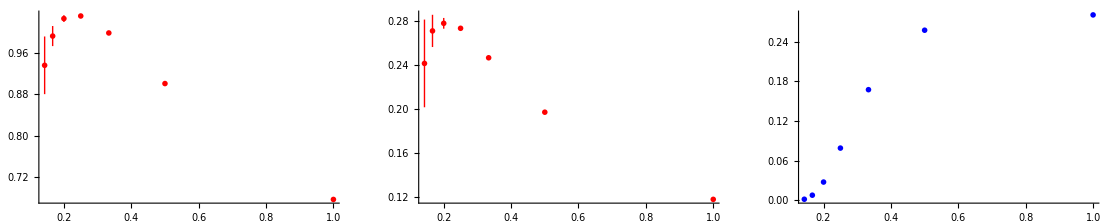

2.8

G:\LAT\sd_metropolis\data\pcm_sc_mspace\scalars_d2_t8_s8_l4.0000_m-1.20_rsm.dat

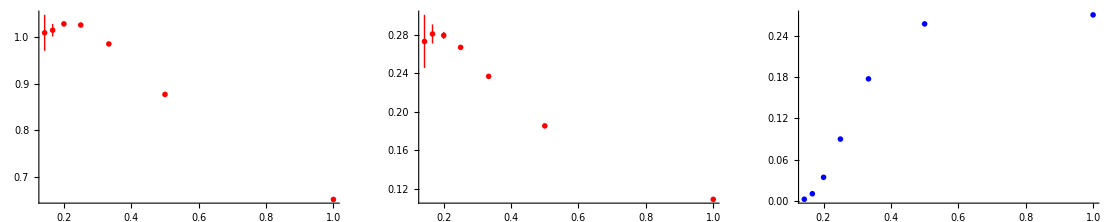

```mathematica
Get["G:\\LAT\\sd_metropolis\\convergence_analysis.m"];
Do[
meff2=-4.0 + m0;
Print[m0];
ScalarsFile="G:\\LAT\\sd_metropolis\\data\\pcm_sc_mspace\\scalars_d2_t8_s8_l4.0000_m"<>fsndig[meff2,2]<>"_rsm.dat";
Print[ScalarsFile];
SUNData=GetConvergenceData[ScalarsFile,1,2,0.0,1.0,10];
LinkData=GetConvergenceData[ScalarsFile,1,4,0.0,1.0,10];
LinkSPData=GetConvergenceData[ScalarsFile,1,5,0.0,1.0,10];
RCANData={{1/1,0.38095238095238093},{1/2,0.41715128984322375},{1/3,0.45920358337341727},{1/4,0.46448009338131374},{1/5,0.4773704921241454}};
Gr1=PlotWithErrors[SUNData,Red];
Gr2=PlotWithErrors[LinkData,Red];
Gr3=ListPlot[RCANData,PlotStyle->{Blue}];
Gr4=PlotWithErrors[LinkSPData,Blue];
Print[GraphicsGrid[{{Gr1,Gr2,Gr4}}]];
,{m0,{2.6,2.8}}]
```

```mathematica
N[1/4+1/32]
```

0.28125